# Clear Variables

```mathematica
Clear["Global`*"]
```

# Define and Solve DiffEqs

```mathematica
(*constants*)
g=9.8;
m1=1;
m2=1.5;
k1=50;
k2=50;
c1=5;(*friction coefficients*)
c2=8;
L1=1;(*natural lengths of spring*)
L2=1;

(*initial conditions*)
x01=0;(*initial displacement*)
xd01=0.0;(*initial velocity*)
x02=2.25;
xd02=0.0;

(*IOPNFEWGWIOVOIPEWOIVBNWE:IOBVNWEIO:VBNEWAOU:b*)
(*x1[t_]:=(-m1*a1[t]-c1*v1[t]+k1*L1+k2*x2[t]-k2*L2)/(k1+k2) x2[t_]:=(-m2*a2[t]-c2*v2[t]+k2*x1[t]+k2*L2)/k2 v1[t_]:=(-m1*a1[t]-k1(x1-L1)+k2(x2[t]-x1[t]-L2))/c1 v2[t_]:=(-m2*a2[t]-k2(x2[t]-x1[t]-L2))/c2*)

eqns={x1''[t]==(k2 (x2[t]-x1[t]-L2)-c1*x1'[t]-k1 (x1[t]-L1))/m1,x2''[t]==(-k2 (x2[t]-x1[t]-L2)-c2*x2'[t])/m2,x1[0]==x01,x2[0]==x02,x1'[0]==xd01,x2'[0]==xd02};

sol1=NDSolve[eqns,{x1},{t,0,100000}];
pos1=x1/. First[sol1];
sol2=NDSolve[eqns,{x1'},{t,0,100000}];
vel1=x1'/. First[sol2];
sol3=NDSolve[eqns,{x1''},{t,0,100000}];
acc1=x1''/. First[sol3];
sol4=NDSolve[eqns,{x2},{t,0,100000}];
pos2=x2/. First[sol4];
sol5=NDSolve[eqns,{x2'},{t,0,100000}];
vel2=x2'/. First[sol5];
sol6=NDSolve[eqns,{x2''},{t,0,100000}];
acc2=x2''/. First[sol6];
```

# Plot Functions

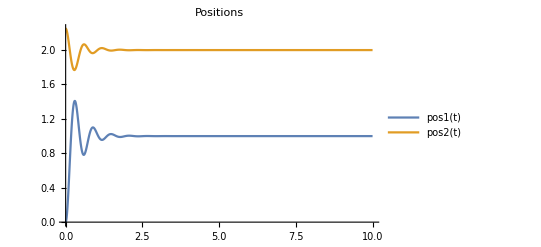

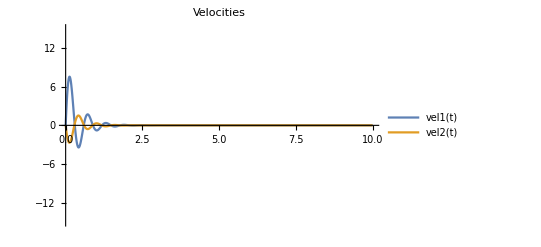

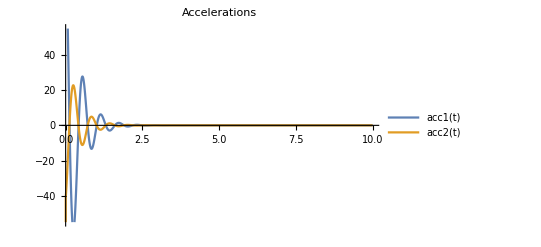

```mathematica
Plot[{pos1[t],pos2[t]},{t,0,10},PlotRange->Automatic,PlotLabel->Style["Positions",FontSize->18],PlotLegends->"Expressions"]
Plot[{vel1[t],vel2[t]},{t,0,10},PlotRange->{-15,15},PlotLabel->Style["Velocities",FontSize->18],PlotLegends->"Expressions"]
Plot[{acc1[t],acc2[t]},{t,0,10},PlotRange->{-55,55},PlotLabel->Style["Accelerations",FontSize->18],PlotLegends->"Expressions"]
```

# Create Bad Animation

```mathematica
ListAnimate[Table[ListPlot[{{pos1[n/60],0},{pos2[n/60],0}},PlotRange->{{-(L1+x01+L2+x02),L1+x01+L2+x02},{-10,10}}],{n,600}]]
```

# Create Cool Animation

```mathematica
Manipulate[
Graphics[
{Translate[{Blue,Rectangle[{0,1},{1,2}]},{pos1[t] *4,0.5}],
Translate[{Red,Rectangle[{0,1},{1,2}]},{pos2[t]*4,0.5}],
Black,Line[{{(pos1[t]*4)+L1,2},{(pos2[t]*4),2}}],
Black,Line[{{0,2},{(pos1[t]*4),2}}]
},
Background->LightYellow,PlotRange->{{0,15},{0,5}},ImageSize->{500,250},Axes->True
],
{{t,0.,"time t"},0.,5,0.01,ControlType->Trigger}
]
```

# Export GIF

```mathematica
title="EPIC SPRING MASS SYSTEM GIF"
data1 =
Table[Graphics[
{Translate[{Blue,Rectangle[{0,1},{1,2}]},{pos1[t] *4,0.5}],
Translate[{Red,Rectangle[{0,1},{1,2}]},{pos2[t]*4,0.5}],
Black,Line[{{(pos1[t]*4)+L1,2},{(pos2[t]*4),2}}],
Black,Line[{{0,2},{(pos1[t]*4),2}}]
},
Background->LightYellow,PlotRange->{{0,15},{0,5}},ImageSize->{500,250},Axes->True
],{t,0,5,.1}];
(*/.(AppearanceElements->_)->(AppearanceElements->{})*)
(*change to your directory*)
SetDirectory["C:\\Users\\gelin\\OneDrive\\Desktop"]
(*the exported GIF SUCKS!!!!!!:*)
Export["spring_animation.gif",data1,"AnimationRepetitions"->∞]
```

EPIC SPRING MASS SYSTEM GIF

C:\Users\gelin\OneDrive\Desktop

spring_animation.gif